```mathematica
SetDirectory[NotebookDirectory[]];
```

## p10q3

```mathematica
datadir="../Processed_Data/7_MagneticCatalysis_AFM";
```

```mathematica
a0v0d75data=Import[StringJoin[datadir,"/p10q3n4a0_U0.75_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d75data=Import[StringJoin[datadir,"/p10q3n4a0.2_U0.75_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d75data=Import[StringJoin[datadir,"/p10q3n4a0.4_U0.75_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d5v0d75data=Import[StringJoin[datadir,"/p10q3n4a0.5_U0.75_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d75data=Import[StringJoin[datadir,"/p10q3n4a0.6_U0.75_AFMOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d8data=Import[StringJoin[datadir,"/p10q3n4a0_U0.8_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d8data=Import[StringJoin[datadir,"/p10q3n4a0.2_U0.8_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d8data=Import[StringJoin[datadir,"/p10q3n4a0.4_U0.8_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d5v0d8data=Import[StringJoin[datadir,"/p10q3n4a0.5_U0.8_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d8data=Import[StringJoin[datadir,"/p10q3n4a0.6_U0.8_AFMOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d85data=Import[StringJoin[datadir,"/p10q3n4a0_U0.85_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d85data=Import[StringJoin[datadir,"/p10q3n4a0.2_U0.85_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d85data=Import[StringJoin[datadir,"/p10q3n4a0.4_U0.85_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d5v0d85data=Import[StringJoin[datadir,"/p10q3n4a0.5_U0.85_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d85data=Import[StringJoin[datadir,"/p10q3n4a0.6_U0.85_AFMOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d75data=a0v0d75data[[;;,Ordering[a0v0d75data[[1]]]]];
a0d2v0d75data=a0d2v0d75data[[;;,Ordering[a0d2v0d75data[[1]]]]];
a0d4v0d75data=a0d4v0d75data[[;;,Ordering[a0d4v0d75data[[1]]]]];
a0d5v0d75data=a0d5v0d75data[[;;,Ordering[a0d5v0d75data[[1]]]]];
a0d6v0d75data=a0d6v0d75data[[;;,Ordering[a0d6v0d75data[[1]]]]];
```

```mathematica
a0v0d8data=a0v0d8data[[;;,Ordering[a0v0d8data[[1]]]]];
a0d2v0d8data=a0d2v0d8data[[;;,Ordering[a0d2v0d8data[[1]]]]];
a0d4v0d8data=a0d4v0d8data[[;;,Ordering[a0d4v0d8data[[1]]]]];
a0d5v0d8data=a0d5v0d8data[[;;,Ordering[a0d5v0d8data[[1]]]]];
a0d6v0d8data=a0d6v0d8data[[;;,Ordering[a0d6v0d8data[[1]]]]];
```

```mathematica
a0v0d85data=a0v0d85data[[;;,Ordering[a0v0d85data[[1]]]]];
a0d2v0d85data=a0d2v0d85data[[;;,Ordering[a0d2v0d85data[[1]]]]];
a0d4v0d85data=a0d4v0d85data[[;;,Ordering[a0d4v0d85data[[1]]]]];
a0d5v0d85data=a0d5v0d85data[[;;,Ordering[a0d5v0d85data[[1]]]]];
a0d6v0d85data=a0d6v0d85data[[;;,Ordering[a0d6v0d85data[[1]]]]];
```

```mathematica
numplaqs=421;
```

```mathematica
psize=0.03;
lthickness=0.006;
```

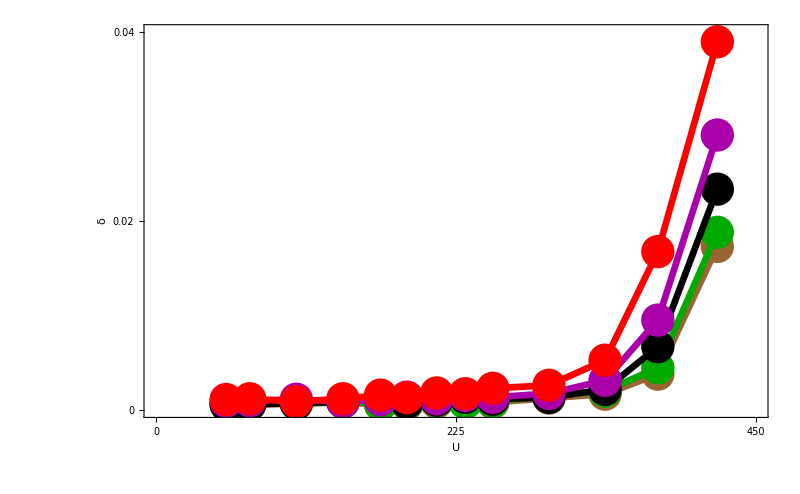

```mathematica
xrange={0,450};
yrange={0,0.04};
Show[
ListPlot[Transpose@{numplaqs*a0v0d75data[[1]],a0v0d75data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d75data[[1]],a0v0d75data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d75data[[1]],a0d2v0d75data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d75data[[1]],a0d2v0d75data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d75data[[1]],a0d4v0d75data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d75data[[1]],a0d4v0d75data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d5v0d75data[[1]],a0d5v0d75data[[2]]},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d5v0d75data[[1]],a0d5v0d75data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d75data[[1]],a0d6v0d75data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d75data[[1]],a0d6v0d75data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.02,0.04},None},{{0,225,450},None}},FrameTicksStyle->FontSize->50
]
```

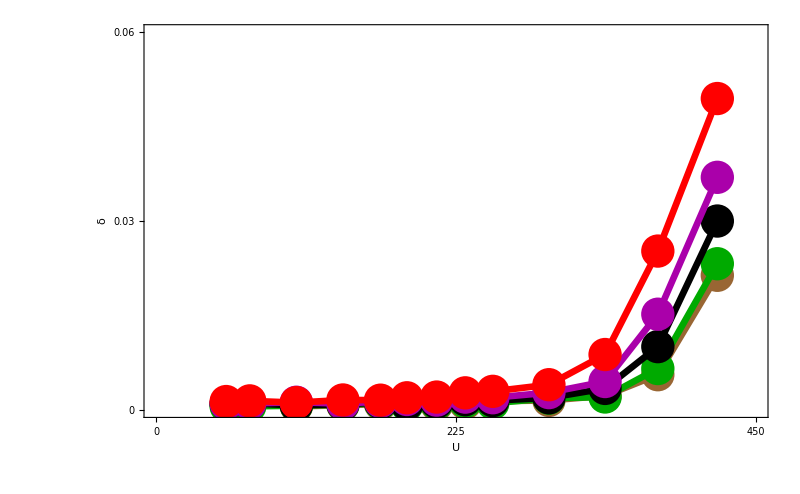

```mathematica
xrange={0,450};
yrange={0,0.06};
Show[
ListPlot[Transpose@{numplaqs*a0v0d8data[[1]],a0v0d8data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d8data[[1]],a0v0d8data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d8data[[1]],a0d2v0d8data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d8data[[1]],a0d2v0d8data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d8data[[1]],a0d4v0d8data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d8data[[1]],a0d4v0d8data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d5v0d8data[[1]],a0d5v0d8data[[2]]},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d5v0d8data[[1]],a0d5v0d8data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d8data[[1]],a0d6v0d8data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d8data[[1]],a0d6v0d8data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.03,0.06},None},{{0,225,450},None}},FrameTicksStyle->FontSize->50
]
```

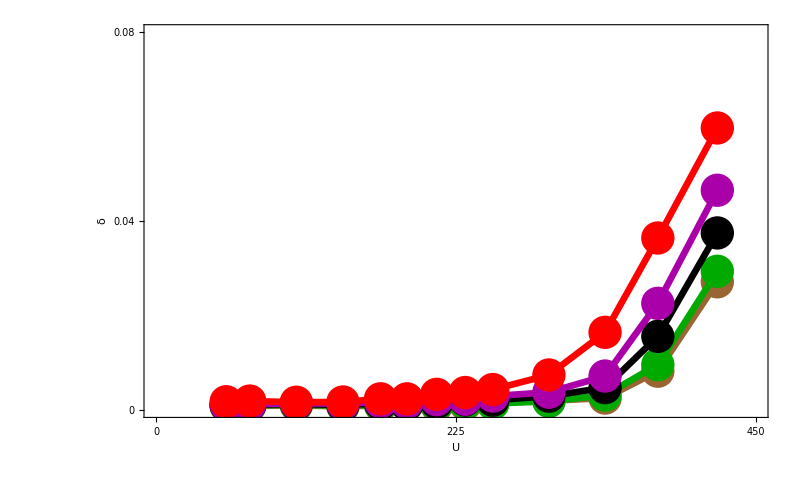

```mathematica
xrange={0,450};
yrange={0,0.08};
Show[
ListPlot[Transpose@{numplaqs*a0v0d85data[[1]],a0v0d85data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d85data[[1]],a0v0d85data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d85data[[1]],a0d2v0d85data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d85data[[1]],a0d2v0d85data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d85data[[1]],a0d4v0d85data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d85data[[1]],a0d4v0d85data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d5v0d85data[[1]],a0d5v0d85data[[2]]},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d5v0d85data[[1]],a0d5v0d85data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d85data[[1]],a0d6v0d85data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d85data[[1]],a0d6v0d85data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.04,0.08},None},{{0,225,450},None}},FrameTicksStyle->FontSize->50
]
```

## p14q3

```mathematica
datadir="../Processed_Data/7_MagneticCatalysis_AFM";
```

```mathematica
a0v0d65data=Import[StringJoin[datadir,"/p14q3n3a0_U0.65_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d65data=Import[StringJoin[datadir,"/p14q3n3a0.2_U0.65_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d65data=Import[StringJoin[datadir,"/p14q3n3a0.4_U0.65_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d65data=Import[StringJoin[datadir,"/p14q3n3a0.6_U0.65_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d7v0d65data=Import[StringJoin[datadir,"/p14q3n3a0.7_U0.65_AFMOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d7data=Import[StringJoin[datadir,"/p14q3n3a0_U0.7_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d7data=Import[StringJoin[datadir,"/p14q3n3a0.2_U0.7_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d7data=Import[StringJoin[datadir,"/p14q3n3a0.4_U0.7_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d7data=Import[StringJoin[datadir,"/p14q3n3a0.6_U0.7_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d7v0d7data=Import[StringJoin[datadir,"/p14q3n3a0.7_U0.7_AFMOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d75data=Import[StringJoin[datadir,"/p14q3n3a0_U0.75_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d75data=Import[StringJoin[datadir,"/p14q3n3a0.2_U0.75_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d75data=Import[StringJoin[datadir,"/p14q3n3a0.4_U0.75_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d75data=Import[StringJoin[datadir,"/p14q3n3a0.6_U0.75_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d7v0d75data=Import[StringJoin[datadir,"/p14q3n3a0.7_U0.75_AFMOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d65data=a0v0d65data[[;;,Ordering[a0v0d65data[[1]]]]];
a0d2v0d65data=a0d2v0d65data[[;;,Ordering[a0d2v0d65data[[1]]]]];
a0d4v0d65data=a0d4v0d65data[[;;,Ordering[a0d4v0d65data[[1]]]]];
a0d6v0d65data=a0d6v0d65data[[;;,Ordering[a0d6v0d65data[[1]]]]];
a0d7v0d65data=a0d7v0d65data[[;;,Ordering[a0d7v0d65data[[1]]]]];
```

```mathematica
a0v0d7data=a0v0d7data[[;;,Ordering[a0v0d7data[[1]]]]];
a0d2v0d7data=a0d2v0d7data[[;;,Ordering[a0d2v0d7data[[1]]]]];
a0d4v0d7data=a0d4v0d7data[[;;,Ordering[a0d4v0d7data[[1]]]]];
a0d6v0d7data=a0d6v0d7data[[;;,Ordering[a0d6v0d7data[[1]]]]];
a0d7v0d7data=a0d7v0d7data[[;;,Ordering[a0d7v0d7data[[1]]]]];
```

```mathematica
a0v0d75data=a0v0d75data[[;;,Ordering[a0v0d75data[[1]]]]];
a0d2v0d75data=a0d2v0d75data[[;;,Ordering[a0d2v0d75data[[1]]]]];
a0d4v0d75data=a0d4v0d75data[[;;,Ordering[a0d4v0d75data[[1]]]]];
a0d6v0d75data=a0d6v0d75data[[;;,Ordering[a0d6v0d75data[[1]]]]];
a0d7v0d75data=a0d7v0d75data[[;;,Ordering[a0d7v0d75data[[1]]]]];
```

```mathematica
numplaqs=155;
```

```mathematica
psize=0.03;
lthickness=0.006;
```

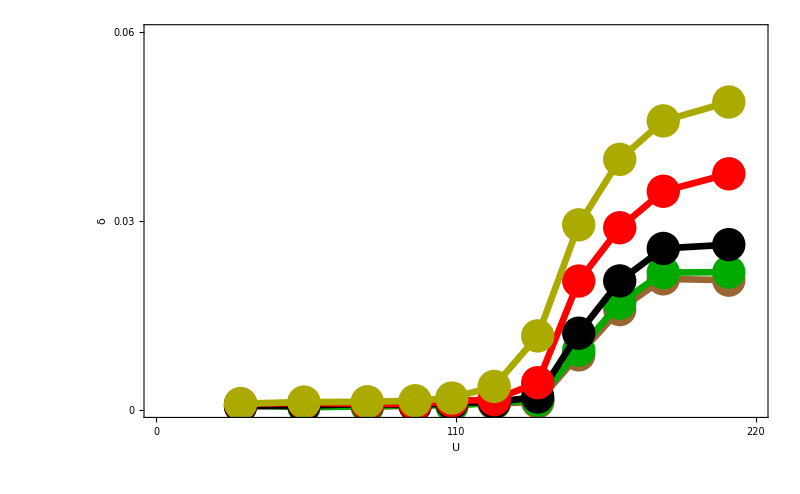

```mathematica
xrange={0,220};
yrange={0,0.06};
Show[
ListPlot[Transpose@{numplaqs*a0v0d65data[[1]],a0v0d65data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d65data[[1]][[;;-5]],a0v0d65data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d65data[[1]],a0d2v0d65data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d65data[[1]][[;;-5]],a0d2v0d65data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d65data[[1]],a0d4v0d65data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d65data[[1]][[;;-5]],a0d4v0d65data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d65data[[1]],a0d6v0d65data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d65data[[1]][[;;-5]],a0d6v0d65data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d7v0d65data[[1]],a0d7v0d65data[[2]]},PlotStyle->{Darker[Yellow],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d7v0d65data[[1]][[;;-5]],a0d7v0d65data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Yellow],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.03,0.06},None},{{0,110,220},None}},FrameTicksStyle->FontSize->50
]
```

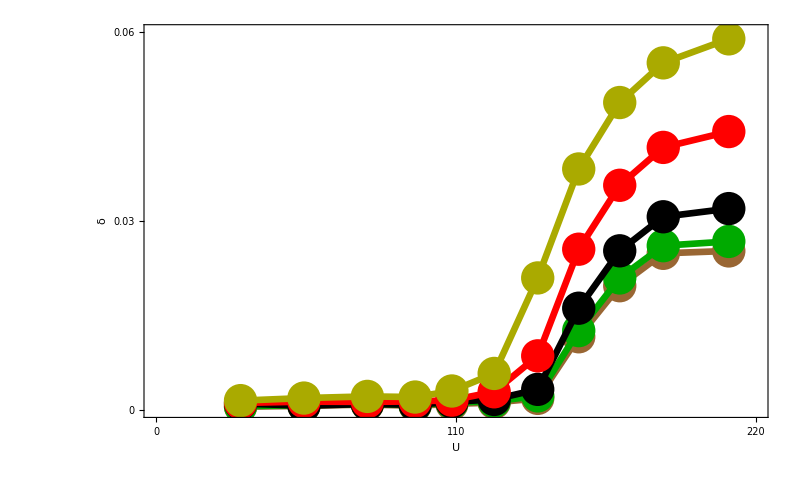

```mathematica
xrange={0,220};
yrange={0,0.06};
Show[
ListPlot[Transpose@{numplaqs*a0v0d7data[[1]],a0v0d7data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d7data[[1]][[;;-5]],a0v0d7data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d7data[[1]],a0d2v0d7data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d7data[[1]][[;;-5]],a0d2v0d7data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d7data[[1]],a0d4v0d7data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d7data[[1]][[;;-5]],a0d4v0d7data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d7data[[1]],a0d6v0d7data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d7data[[1]][[;;-5]],a0d6v0d7data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d7v0d7data[[1]],a0d7v0d7data[[2]]},PlotStyle->{Darker[Yellow],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d7v0d7data[[1]][[;;-5]],a0d7v0d7data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Yellow],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.03,0.06},None},{{0,110,220},None}},FrameTicksStyle->FontSize->50
]
```

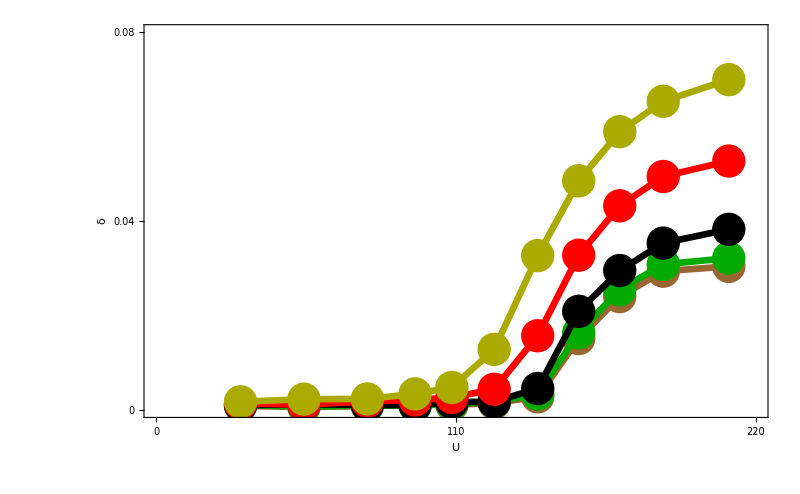

```mathematica
xrange={0,220};
yrange={0,0.08};
Show[
ListPlot[Transpose@{numplaqs*a0v0d75data[[1]],a0v0d75data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d75data[[1]][[;;-5]],a0v0d75data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d75data[[1]],a0d2v0d75data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d75data[[1]][[;;-5]],a0d2v0d75data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d75data[[1]],a0d4v0d75data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d75data[[1]][[;;-5]],a0d4v0d75data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d75data[[1]],a0d6v0d75data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d75data[[1]][[;;-5]],a0d6v0d75data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d7v0d75data[[1]],a0d7v0d75data[[2]]},PlotStyle->{Darker[Yellow],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d7v0d75data[[1]][[;;-5]],a0d7v0d75data[[2]][[;;-5]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Yellow],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.04,0.08},None},{{0,110,220},None}},FrameTicksStyle->FontSize->50
]
```

## Honeycomb

```mathematica
datadir="../Processed_Data/7_MagneticCatalysis_AFM";
```

```mathematica
a0v0d9data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0_U0.9_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d9data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.2_U0.9_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d9data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.4_U0.9_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d9data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.6_U0.9_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d8v0d9data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.8_U0.9_AFMOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v1data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0_U1_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v1data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.2_U1_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v1data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.4_U1_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v1data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.6_U1_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d8v1data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.8_U1_AFMOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v1d1data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0_U1.1_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v1d1data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.2_U1.1_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v1d1data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.4_U1.1_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v1d1data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.6_U1.1_AFMOrderFunctionMagneticFlux.txt"],"Data"];
a0d8v1d1data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.8_U1.1_AFMOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d9data=a0v0d9data[[;;,Ordering[a0v0d9data[[1]]]]];
a0d2v0d9data=a0d2v0d9data[[;;,Ordering[a0d2v0d9data[[1]]]]];
a0d4v0d9data=a0d4v0d9data[[;;,Ordering[a0d4v0d9data[[1]]]]];
a0d6v0d9data=a0d6v0d9data[[;;,Ordering[a0d6v0d9data[[1]]]]];
a0d8v0d9data=a0d8v0d9data[[;;,Ordering[a0d8v0d9data[[1]]]]];
```

```mathematica
a0v1data=a0v1data[[;;,Ordering[a0v1data[[1]]]]];
a0d2v1data=a0d2v1data[[;;,Ordering[a0d2v1data[[1]]]]];
a0d4v1data=a0d4v1data[[;;,Ordering[a0d4v1data[[1]]]]];
a0d6v1data=a0d6v1data[[;;,Ordering[a0d6v1data[[1]]]]];
a0d8v1data=a0d8v1data[[;;,Ordering[a0d8v1data[[1]]]]];
```

```mathematica
a0v1d1data=a0v1d1data[[;;,Ordering[a0v1d1data[[1]]]]];
a0d2v1d1data=a0d2v1d1data[[;;,Ordering[a0d2v1d1data[[1]]]]];
a0d4v1d1data=a0d4v1d1data[[;;,Ordering[a0d4v1d1data[[1]]]]];
a0d6v1d1data=a0d6v1d1data[[;;,Ordering[a0d6v1d1data[[1]]]]];
a0d8v1d1data=a0d8v1d1data[[;;,Ordering[a0d8v1d1data[[1]]]]];
```

```mathematica
numplaqs=1141;
```

```mathematica
psize=0.03;
lthickness=0.006;
```

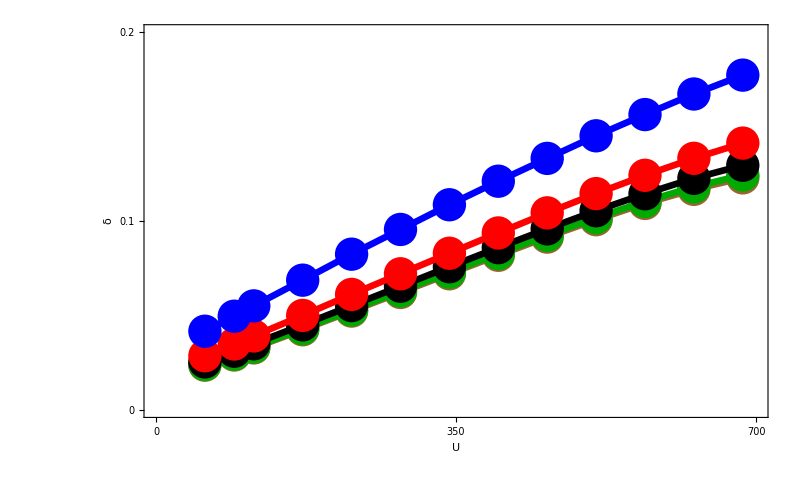

```mathematica
xrange={0,700};
yrange={0,0.2};
Show[
ListPlot[Transpose@{numplaqs*a0v0d9data[[1]],a0v0d9data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d9data[[1]],a0v0d9data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d9data[[1]],a0d2v0d9data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d9data[[1]],a0d2v0d9data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d9data[[1]],a0d4v0d9data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d9data[[1]],a0d4v0d9data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d9data[[1]],a0d6v0d9data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d9data[[1]],a0d6v0d9data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d8v0d9data[[1]],a0d8v0d9data[[2]]},PlotStyle->{Blue,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d8v0d9data[[1]],a0d8v0d9data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.1,0.2},None},{{0,350,700},None}},FrameTicksStyle->FontSize->50
]
```

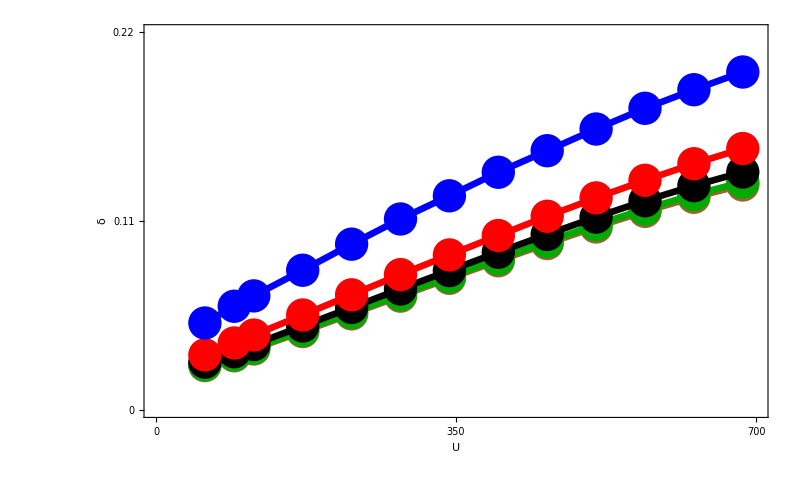

```mathematica
xrange={0,700};
yrange={0,0.22};
Show[
ListPlot[Transpose@{numplaqs*a0v1data[[1]],a0v1data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v1data[[1]],a0v1data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v1data[[1]],a0d2v1data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v1data[[1]],a0d2v1data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v1data[[1]],a0d4v1data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v1data[[1]],a0d4v1data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v1data[[1]],a0d6v1data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v1data[[1]],a0d6v1data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d8v1data[[1]],a0d8v1data[[2]]},PlotStyle->{Blue,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d8v1data[[1]],a0d8v1data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.11,0.22},None},{{0,350,700},None}},FrameTicksStyle->FontSize->50
]
```

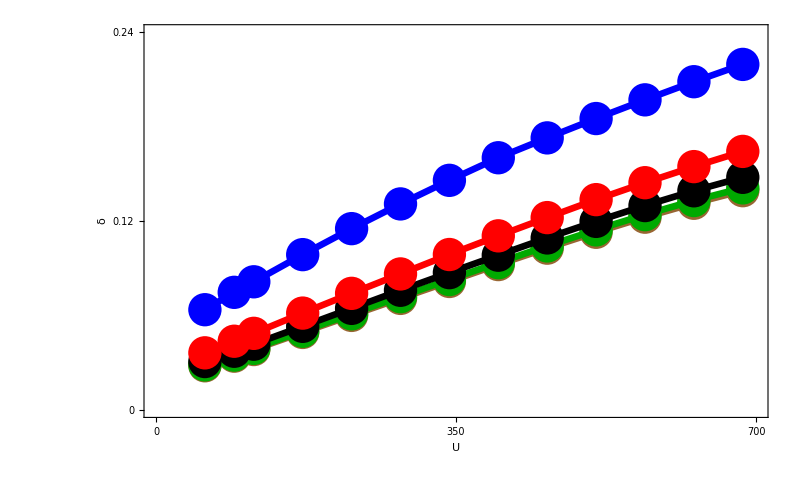

```mathematica
xrange={0,700};
yrange={0,0.24};
Show[
ListPlot[Transpose@{numplaqs*a0v1d1data[[1]],a0v1d1data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v1d1data[[1]],a0v1d1data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v1d1data[[1]],a0d2v1d1data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v1d1data[[1]],a0d2v1d1data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v1d1data[[1]],a0d4v1d1data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v1d1data[[1]],a0d4v1d1data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v1d1data[[1]],a0d6v1d1data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v1d1data[[1]],a0d6v1d1data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d8v1d1data[[1]],a0d8v1d1data[[2]]},PlotStyle->{Blue,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d8v1d1data[[1]],a0d8v1d1data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.12,0.24},None},{{0,350,700},None}},FrameTicksStyle->FontSize->50
]
```